# Low rank approximations

We have seen how the singular value decomposition can be used to identify the “most important” information in a matrix by choosing the “best” low-rank approximation. One application of this idea is in the area of image compression, where we would like to represent the matrix of pixels in an image in an efficient way.

## Flags

For image compression, the use of the singular value decomposition will be particularly effective in images where there are a lot of horizontal and vertical lines. National flags make perfect examples as many of them can be represented by low-rank matrices. Before we start, consider each of the flags below. Can you put them in order of rank? Can you predict the rank for each of the low-rank cases?

```mathematica
countries={"Ireland","Norway","Germany","Finland","United Kingdom","Czech Republic","Greece","Japan","Nepal","Thailand","Madagascar","Tanzania"};
```

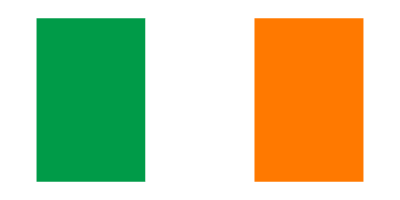
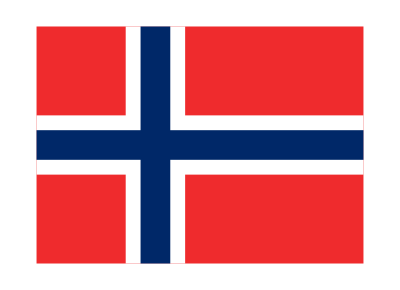

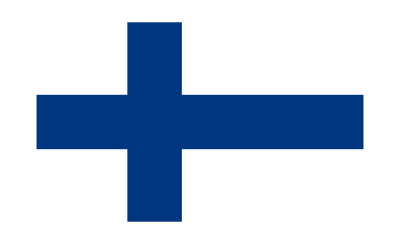

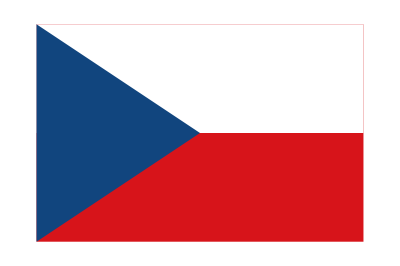
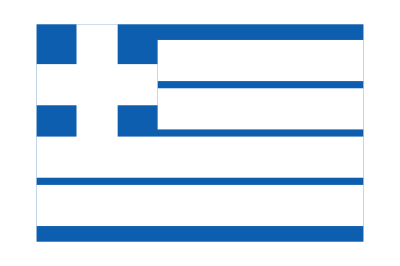

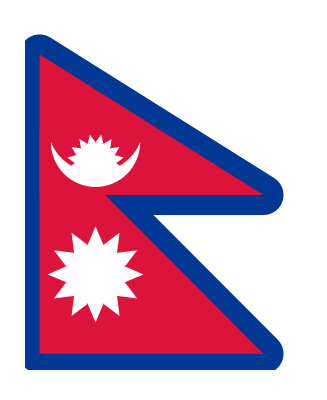
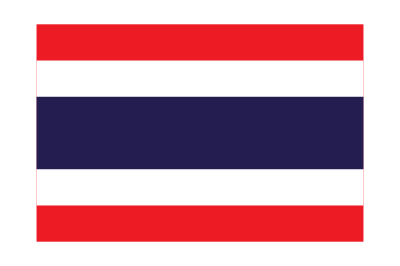
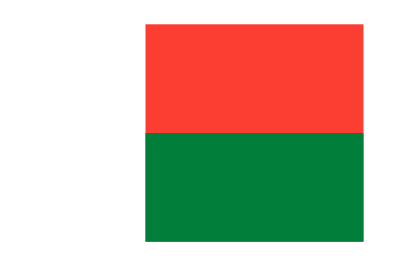
{-Graphics-Ireland,-Graphics-Norway,-Graphics-Germany,-Graphics-Finland,-Graphics-United Kingdom,-Graphics-Czech Republic,-Graphics-Greece,-Graphics-Japan,-Graphics-Nepal,-Graphics-Thailand,-Graphics-Madagascar,-Graphics-Tanzania}

```mathematica
Table[Labeled[Framed[CountryData[country,"Flag"]],country],{country,countries}]
```

```mathematica
flagRank[country_]:=MatrixRank[ImageData[ColorConvert[CountryData[country,"Flag"],"Grayscale"],Interleaving->False][[1]],Tolerance->10^-3];
```

```mathematica
sortedCountries=SortBy[countries,flagRank]
```

{Germany,Ireland,Thailand,Madagascar,Finland,Greece,Norway,Japan,Czech Republic,United Kingdom,Nepal,Tanzania}

```mathematica
Table[Labeled[Framed[CountryData[country,"Flag"]],country<>": "<>ToString[flagRank[country]]],{country,sortedCountries}]
```

{-Graphics-Germany: 1,-Graphics-Ireland: 1,-Graphics-Thailand: 1,-Graphics-Madagascar: 2,-Graphics-Finland: 3,-Graphics-Greece: 4,-Graphics-Norway: 4,-Graphics-Japan: 39,-Graphics-Czech Republic: 72,-Graphics-United Kingdom: 74,-Graphics-Nepal: 112,-Graphics-Tanzania: 140}

### Rank-1 flags

Let’s first look at one of the good cases: Ireland. We’ll begin by loading the Irish flag from Mathematica’s CountryData:

```mathematica
flag=ImageCrop[CountryData["Ireland","Flag"]]
```

-Graphics-

```mathematica
ImageDimensions[flag]
```

{214,107}

This is an image built up out pixels represented by a matrix of size 127 x 255. Each entry in the matrix contains three numbers, one each representing how much of red, green and blue is present in that pixel. For simplicity, let’s convert these three numbers to a single number by converting the colour image to grayscale.

```mathematica
flagBW=ColorConvert[flag,"Grayscale"]
```

-Graphics-

Next we translate this image into 127 x 255 matrix of numbers in the range [0,1] where 0 represents black and 1 represents white.

```mathematica
flagMatrix=ImageData[flagBW,Interleaving->False][[1]];
```

```mathematica
NumberForm[MatrixForm[Downsample[flagMatrix,20]],1]
```

(0.4 | 0.4 | 0.4 | 0.4 | 1. | 1. | 1. | 1. | 0.6 | 0.6 | 0.6
0.4 | 0.4 | 0.4 | 0.4 | 1. | 1. | 1. | 1. | 0.6 | 0.6 | 0.6
0.4 | 0.4 | 0.4 | 0.4 | 1. | 1. | 1. | 1. | 0.6 | 0.6 | 0.6
0.4 | 0.4 | 0.4 | 0.4 | 1. | 1. | 1. | 1. | 0.6 | 0.6 | 0.6
0.4 | 0.4 | 0.4 | 0.4 | 1. | 1. | 1. | 1. | 0.6 | 0.6 | 0.6
0.4 | 0.4 | 0.4 | 0.4 | 1. | 1. | 1. | 1. | 0.6 | 0.6 | 0.6)

Now that we have a matrix, we can compute its singular value decomposition:

```mathematica
{U,Σ,V}=SingularValueDecomposition[flagMatrix];
σ=Diagonal[Σ];
```

We can reconstruct the original matrix and image from these:

```mathematica
Image[U.Σ.Transpose[V]]
```

-Graphics-

Let’s look at the singular values, to see how many important singular vectors there are:

```mathematica
σ
```

{106.298,0.0525629,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

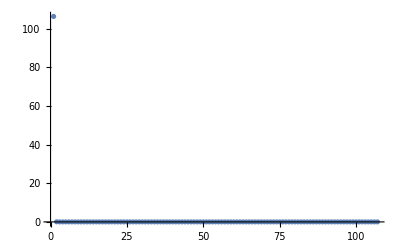

```mathematica
ListPlot[σ]
```

This is a particularly nice matrix since it only has one singular value. It is therefore rank-1 and we have a very efficient low-rank approximation that is exact!

```mathematica
Image[σ[[1]]U[[All,1]]⊗V[[All,1]]]
```

-Graphics-

```mathematica
Max[Abs[σ[[1]]U[[All,1]]⊗V[[All,1]]-flagMatrix]]
```

0.043735

This represents the flag by the first singular vector in U, which is just a vector with the same number 127 times. This tells us that the flag doesn’t change along the vertical.

```mathematica
U[[All,1]]
```

{-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0966765,-0.0963708}

The first singular vector in V is just a 255 element vector of three numbers, representing the darkness of each of the three bands that change along the horizontal.

```mathematica
V[[All,1]]
```

{-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.03778,-0.0896372,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0973086,-0.0663799,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.0560976,-0.055716}

### Higher rank flags

Other flags are less simple than the Irish flag. Let’s try to figure out what rank the Greek flag is.

Let’s load the Greek flag from Mathematica’s CountryData:

```mathematica
flag=ImageCrop[CountryData["Greece","Flag"]]
```

-Graphics-

```mathematica
ImageDimensions[flag]
```

{213,142}

Now convert the colour image to grayscale.

```mathematica
flagBW=ColorConvert[flag,"Grayscale"]
```

-Graphics-

Next we translate this image into 169 x 255 matrix of numbers in the range [0,1] where 0 represents black and 1 represents white.

```mathematica
flagMatrix=ImageData[flagBW,Interleaving->False][[1]];
```

Now that we have a matrix, we can compute its singular value decomposition:

```mathematica
{U,Σ,V}=SingularValueDecomposition[flagMatrix];
σ=Diagonal[Σ];
```

It looks like there are only 3 (or maybe 6) singular values:

```mathematica
σ
```

{116.751,29.0585,14.1208,0.119766,0.104447,0.0421435,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

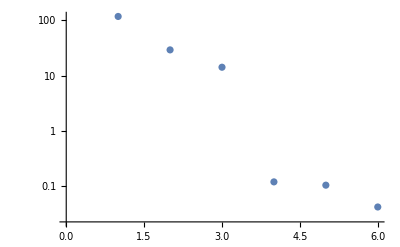

```mathematica
ListLogPlot[σ]
```

We can reconstruct the original matrix and image from the full set:

```mathematica
Image[U.Σ.Transpose[V]]
```

-Graphics-

We can see how this is built up from three rank-1 matrices:

```mathematica
Table[Image[(σ[[i]]U[[All,i]]⊗V[[All,i]])/Max[σ[[i]]U[[All,i]]⊗V[[All,i]]]],{i,6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Medium rank flags

The Japanese flag is an example of a medium rank case. Let’s first work its SVD

```mathematica
Framed[flag=CountryData["Japan","Flag"]]
```

-Graphics-

```mathematica
flagBW=ColorConvert[flag,"Grayscale"]
```

-Graphics-

```mathematica
flagMatrix=ImageData[flagBW,Interleaving->False][[1]];
```

```mathematica
{U,Σ,V}=SingularValueDecomposition[flagMatrix];
σ=Diagonal[Σ];
```

There are only about 30-40 singular values:

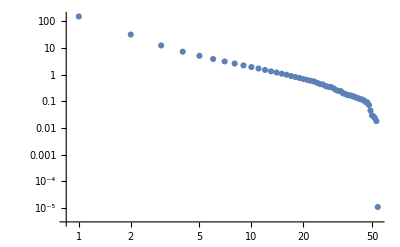

```mathematica
ListLogLogPlot[σ]
```

We can try to understand how the flag is built up by looking at its rank-1 pieces

```mathematica
Table[Image[(σ[[i]]U[[All,i]]⊗V[[All,i]])/Max[σ[[i]]U[[All,i]]⊗V[[All,i]]]],{i,40}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[Image[Sum[σ[[i]]U[[All,i]]⊗V[[All,i]],{i,r}]],{r,1,100,1}]
```

### Full rank flags

It doesn’t take much of a change to turn a nice and simple low-rank flag into something full-rank. Take the Scottish flag, for example:

```mathematica
scotlandFlag=ImageResize[-Graphics-,425];
```

```mathematica
ImageDimensions[scotlandFlag]
```

{425,255}

This looks just as simple as the other flags, but from the point of view of the SVD those diagonal lines are a disaster.

```mathematica
scotlandFlagBW=ColorConvert[scotlandFlag,"Grayscale"]
```

-Graphics-

```mathematica
flagMatrix=ImageData[scotlandFlagBW,Interleaving->False];
```

```mathematica
{U,Σ,V}=SingularValueDecomposition[flagMatrix];
σ=Diagonal[Σ];
```

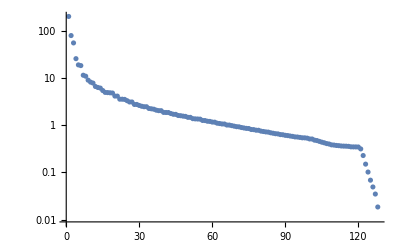

```mathematica
ListLogPlot[σ]
```

```mathematica
Manipulate[Image[Sum[σ[[i]]U[[All,i]]⊗V[[All,i]],{i,r}]],{r,1,100,1}]
```

```mathematica
Table[Image[(σ[[i]]U[[All,i]]⊗V[[All,i]])/Max[σ[[i]]U[[All,i]]⊗V[[All,i]]]],{i,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Given that we know that this should be a simple one, is there something that we can do to make the SVD see it? How about if we rotate the image by π/2 first to transform diagonal lines to horizontal and vertical, and then do the SVD on the rotated image.

First, let’s resize and rotate the flag

```mathematica
scotlandFlagRotated=ImageCrop[ImageRotate[ImageResize[scotlandFlagBW,{255,255}],π/4,Masking->Full],300]
```

-Graphics-

```mathematica
flagMatrixRotated=ImageData[scotlandFlagRotated,Interleaving->False];
```

Now compute the SVD

```mathematica
{UR,ΣR,VR}=SingularValueDecomposition[flagMatrixRotated];
σR=Diagonal[ΣR];
```

We can check that the singular values now fall off quite a bit faster

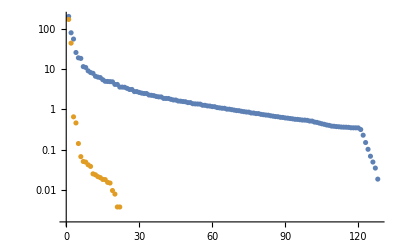

```mathematica
ListLogPlot[{σ,σR}]
```

Now reconstruct the original flag.

```mathematica
Manipulate[ImageResize[ImageRotate[Image[Sum[σR[[i]]UR[[All,i]]⊗VR[[All,i]],{i,r}]],-π/4,"MaxAreaCropping"],{255,127}],{r,1,100,1}]
```

We see that it’s almost perfectly rank-2!

## Image compression

Compression using singular values can also be achieve with more complicated images. Let’s try it with a photo of UCD. First, we load the image and convert it to grayscale

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
img=ColorConvert[Import["UCD.jpg"],"Grayscale"]
```

-Graphics-

Now convert the grayscale image to a matrix of pixel values.

```mathematica
imgData=ImageData[img];
```

Next, compute the SVD:

```mathematica
{U,Σ,V}=SingularValueDecomposition[imgData];
σ=Diagonal[Σ];
```

We can reconstruct the original image from the full SVD

```mathematica
Image[U.Σ.Transpose[V]]
```

-Graphics-

We can also get a pretty good approximation by only including the largest singular values and vectors

```mathematica
Manipulate[Labeled[Image[U[[All,1;;n]].Σ[[1;;n,1;;n]].Transpose[V[[All,1;;n]]],ImageSize->Full],Row[{n Length[U]+n+n Length[V],"/",Length[U]Length[V]}]],{n,1,Length[Σ],1}]
```

If we plot the singular values, we see that they drop off rapidly until about the 100th value. This suggests that stopping around rank-100 is a good choice.

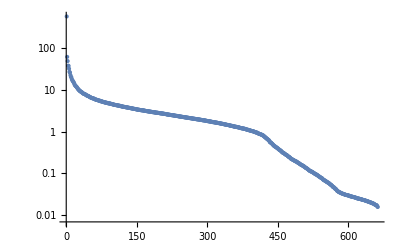

```mathematica
ListLogPlot[Diagonal[Σ],PlotRange->All]
```

```mathematica
With[{n=100},ImageDifference[Image[U[[All,1;;n]].Σ[[1;;n,1;;n]].Transpose[V[[All,1;;n]]]],img]]
```

-Graphics-

## Singular value decomposition for approximating functions

The singular value decomposition does not only apply to linear algebra. We can also use it to get an approximation to an arbitrary function. For example, say we have a functional m_n(x), which is parametrized by n, and for each n we get a function of x. A simple example is m_n(x)=sin(n x) with 0≤n≤10. In reality, this could be a much more complicated function that we would like to approximate in terms of simple functions. In our example, we wish to approximate it by a linear combination of sin(n x) (i.e. basis functions) for specific values of n. The question then is how many specific values of n do we need in our basis so that we can  faithfully reproduce the function for all n? We can answer this question using the singular value decomposition. For this to work, it is important that the function has sufficiently many points in the x direction such that it is resolved. The number of singular values gives the number of basis functions required. These will all be of the same order. Once enough basis functions are included, any further singular values should decrease exponentially in magnitude.

Let’s evaluate our function on a grid:

```mathematica
{Uf,Σf,Vf}=SingularValueDecomposition[Table[N[Sin[n x]],{x,0,2 π,2 π/100},{n,0,10,10/100}]];
σf=Diagonal[Σf];
```

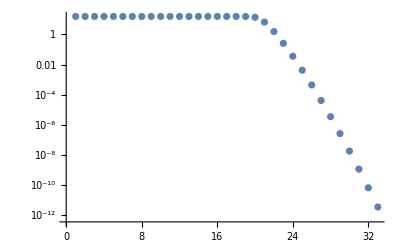

```mathematica
ListLogPlot[σf]
```

We see that in our sin(n x) example, computing the singular values reveals that it is sufficient to have ~20 basis functions in order to reconstruct any value in the range 0≤n≤10.